# Question 2:

```mathematica
(* Defining Constants *)
a0=Quantity["BohrRadius"]//UnitConvert[#,"Angstroms"]&//QuantityMagnitude;
(* Defining functions *)
STO[z_, r_]:= 2z Sqrt[z]Exp[-z r];
GWave[ai_, r_]:=(2ai/π)^(3/4)Exp[-ai r^2];
STO3G[c1_,c2_,c3_,a1_,a2_,a3_,r_]:=
Plus@@(#1GWave[#2,r]&@@@{{c1,a1},{c2,a2},{c3,a3}});
```

## A. Hydrogen fitting

{c1→2.7838032,c2→1.0796892,c3→0.087015687,a1→0.19031241,a2→1.1790845,a3→15.300434}

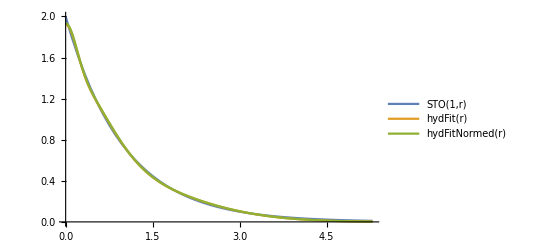

```mathematica
(* Caching data points *)
hydTable=Table[{r, STO[1,r]},{r,0, 10a0, 10a0/200}];

(* Fitting functions *)
hydFit=NonlinearModelFit[
hydTable,{STO3G[c1,c2,c3,a1,a2,a3,r],
{c1≥0,c2≥ 0,c3≥ 0,a1≥ 0,a2≥0,a3≥ 0}},
{c1,c2,c3,a1,a2,a3},r,
MaxIterations->10000];

hydFit["BestFitParameters"]

hydNormFactor=Integrate[hydFit[r]^2 r^2,{r,0,Infinity}];
hydFitNormed[r_]:=hydFit[r]/hydNormFactor;

(* Plot the result *)
Plot[{STO[1,r],hydFit[r], hydFitNormed[r]},
{r,0, 10a0},PlotLegends->"Expressions"]
```

## B. Boron fitting

{c1→2.893,c2→0.0596613,c3→0.979043,a1→4.43101,a2→532.671,a3→30.2264}

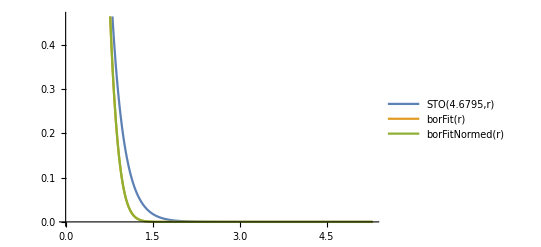

```mathematica
(* Caching data points. For boron, z=4.6795 *)
borTable=Table[{r, STO[4.6795,r]},{r,0, 10a0, 10a0/200}];

(* Fitting functions *)
borFit=NonlinearModelFit[
borTable,{STO3G[c1,c2,c3,a1,a2,a3,r],
{c1≥0,c2≥ 0,c3≥ 0,a1≥ 0,a2≥0,a3≥ 0}},
{c1,c2,c3,a1,a2,a3},r,
MaxIterations->10000];

borFit["BestFitParameters"]

borNormFactor=Integrate[borFit[r]^2 r^2,{r,0,Infinity}];
borFitNormed[r_]:=borFit[r]/borNormFactor;

(* Plot the result *)
Plot[{STO[4.6795,r],borFit[r], borFitNormed[r]},
{r,0, 10a0},PlotLegends->"Expressions"]
```